```mathematica
Quit[]
```

```mathematica
$Assumptions=α∈Reals&&α>0&&m∈Reals&&m>0&&λ∈Reals;
```

```mathematica
ω[p_]:=√(m^2+p^2)-m(*p^2/(2m)*);Nx=15;max=100;
```

```mathematica
m =500/2;λ=π/2;
```

```mathematica
Clear@α
```

```mathematica
α=(*0.33375*)0.10823036071230166;
```

```mathematica
ϕ[n_][p_]:=√(α/(√π 2^n n!)) HermiteH[n,α p] E^(1/2 (-α^2) p^2)
```

```mathematica
H[n_][p_?NumberQ]:=ω[p]ϕ[n][p]-λ/π NIntegrate[(ϕ[n][k]-ϕ[n][p]-(k-p)ϕ[n]'[p])/(p-k)^2,{k,-max,0,max}]
```

```mathematica
Table[2NIntegrate[ϕ[2i+1][p]H[2n+1][p],{p,0,max},MaxRecursion->10],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
Sort@Eigenvalues[Last[%]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {23.632}. NIntegrate obtained -0.000317496 and 3.82191×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {23.632}. NIntegrate obtained -0.000411767 and 4.98176×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {31.3469}. NIntegrate obtained -0.000522111 and 6.44225×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{5466.74,{{0.442658,0.118049,-0.0177524,-0.00810753,-0.00477681,-0.00318813,-0.00229729,-0.00174381,-0.00137454,-0.0011149,-0.000924826,-0.000781157,-0.000669703,-0.000581355,-0.000510039,-0.00045157},{0.142721,0.87909,0.250619,-0.0238054,-0.0105346,-0.00613605,-0.00406409,-0.00291235,-0.00220145,-0.00172959,-0.00139919,-0.00115813,-0.000976447,-0.000835839,-0.000724615,-0.000634992},{-0.0175907,0.295931,1.29085,0.388133,-0.0286911,-0.0123581,-0.00714078,-0.00470329,-0.00335631,-0.00252874,-0.0019815,-0.0015995,-0.00132153,-0.0011125,-0.000951039,-0.000823534},{-0.00810471,-0.0233683,0.454193,1.68992,0.528134,-0.0331058,-0.0139024,-0.00798434,-0.00523653,-0.00372458,-0.0027988,-0.00218836,-0.00176328,-0.00145461,-0.0012229,-0.00104422},{-0.00477673,-0.0105244,-0.0278432,0.615162,2.08081,0.669585,-0.037296,-0.0152775,-0.00873059,-0.00570648,-0.00404808,-0.0030353,-0.00236897,-0.00190587,-0.00157015,-0.00131853},{-0.00318812,-0.0061357,-0.0123333,-0.0317021,0.777834,2.46578,0.811926,-0.041386,-0.0165376,-0.00940984,-0.00613302,-0.00434111,-0.0032491,-0.00253193,-0.00203427,-0.00167402},{-0.00229729,-0.00406407,-0.00713973,-0.0138526,-0.0351811,0.94167,2.84613,0.954809,-0.0454516,-0.0177149,-0.0100395,-0.0065273,-0.00461158,-0.00344619,-0.00268195,-0.00215235},{-0.00174381,-0.00291235,-0.00470323,-0.00798185,-0.0151889,-0.0383933,1.10634,3.22271,1.098,-0.0495443,-0.0188313,-0.0106309,-0.00689638,-0.00486447,-0.00363028,-0.00282199},{-0.00137454,-0.00220145,-0.00335631,-0.00523637,-0.00872544,-0.016392,-0.0414015,1.27163,3.5961,1.24134,-0.0537029,-0.0199036,-0.0111922,-0.00724515,-0.00510304,-0.00380392},{-0.0011149,-0.00172959,-0.00252874,-0.00372457,-0.00570611,-0.00940015,-0.0174894,-0.0442434,1.4374,3.96673,1.3847,-0.057959,-0.0209452,-0.0117299,-0.00757706,-0.00532992},{-0.000924826,-0.00139919,-0.0019815,-0.0027988,-0.00404805,-0.00613222,-0.0100225,-0.0184973,-0.0469421,1.60352,4.33492,1.52799,-0.0623394,-0.0219684,-0.0122489,-0.00789559},{-0.000781157,-0.00115813,-0.0015995,-0.00218836,-0.0030353,-0.00434103,-0.00652572,-0.0106026,-0.0194207,-0.0495113,1.76993,4.7009,1.67111,-0.066869,-0.0229841,-0.0127557},{-0.000669703,-0.000976447,-0.00132153,-0.00176328,-0.00236897,-0.00324909,-0.00461141,-0.00689346,-0.0111456,-0.02028,-0.0519582,1.93657,5.06488,1.814,-0.0715708,-0.0240061},{-0.000581355,-0.00083584,-0.0011125,-0.00145461,-0.00190587,-0.00253021,-0.00344617,-0.00486412,-0.00724,-0.0116603,-0.0210632,-0.054285,2.10339,5.427,1.95662,-0.0764715},{-0.000510039,-0.000724614,-0.000951038,-0.0012229,-0.00157016,-0.00203424,-0.00268196,-0.00363026,-0.00509823,-0.00756848,-0.0121449,-0.0217754,-0.0564899,2.27037,5.78741,2.09889},{-0.000451571,-0.000634993,-0.000823535,-0.00104422,-0.00131852,-0.00167564,-0.00215234,-0.00282198,-0.00380262,-0.00532863,-0.00788111,-0.0126024,-0.0224147,-0.0585673,2.43747,6.14619}}}

{0.393399,0.692045,0.936945,1.15638,1.37936,1.64409,1.96894,2.35773,2.81465,3.34431,3.95661,4.66151,5.48169,6.44147,7.61269,9.10026}

```mathematica
Table[2NIntegrate[ϕ[2i][p]H[2n][p],{p,0,max},MaxRecursion->10],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
Sort@Eigenvalues[Last[%]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {37.4016}. NIntegrate obtained -0.000769647 and 1.03174×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {41.8938}. NIntegrate obtained -0.000929195 and 2.21113×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {41.8938}. NIntegrate obtained -0.00115257 and 2.98699×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{5046.9,{{0.176221,0.0456511,-0.0196862,-0.0107242,-0.00716516,-0.00528691,-0.0041415,-0.00337687,-0.00283369,-0.00242987,-0.00211904,-0.00187315,-0.00167426,-0.0015104,-0.00137332,-0.00125712},{0.0598544,0.660961,0.180538,-0.0231662,-0.0111486,-0.00694286,-0.00488081,-0.00369025,-0.00292851,-0.00240545,-0.00202723,-0.00174278,-0.00152213,-0.00134663,-0.00120415,-0.00108645},{-0.0196147,0.215532,1.08506,0.317489,-0.0275255,-0.0124942,-0.00752824,-0.00515933,-0.00382245,-0.0029836,-0.00241718,-0.00201358,-0.00171392,-0.0014841,-0.00130316,-0.00115759},{-0.0107232,-0.0228831,0.373151,1.49047,0.456974,-0.0317246,-0.0138393,-0.00818103,-0.00552033,-0.00403702,-0.00311636,-0.00250077,-0.00206602,-0.00174582,-0.00150204,-0.00131139},{-0.00716513,-0.0111429,-0.0269005,0.533488,1.88545,0.598068,-0.035789,-0.0151125,-0.008822,-0.00589113,-0.00426958,-0.00327,-0.00260587,-0.00213958,-0.00179802,-0.00153929},{-0.00528691,-0.00694268,-0.0124778,-0.0306175,0.695673,2.27338,0.740179,-0.0397848,-0.0163138,-0.00943656,-0.00625447,-0.00450321,-0.00342874,-0.00271797,-0.002221,-0.00185839},{-0.0041415,-0.0048808,-0.00752761,-0.0138035,-0.0340498,0.85914,2.65604,0.882931,-0.043767,-0.0174538,-0.0100235,-0.00660571,-0.00473236,-0.00358691,-0.00283162,-0.00230514},{-0.00337687,-0.00369025,-0.0051593,-0.00817938,-0.0150453,-0.0372526,1.02353,3.0345,1.02607,-0.0477788,-0.0185443,-0.0105852,-0.00694407,-0.00495515,-0.00374227,-0.0029445},{-0.00283369,-0.00292851,-0.00382245,-0.00552023,-0.00881836,-0.0161992,-0.0402689,1.18861,3.40949,1.1694,-0.0518547,-0.0195966,-0.0111247,-0.00727008,-0.00517112,-0.00389396},{-0.00242987,-0.00240545,-0.0029836,-0.00403701,-0.00589088,-0.00942942,-0.0172714,-0.0431284,1.3542,3.7815,1.31281,-0.0560238,-0.020621,-0.0116455,-0.00758475,-0.00538038},{-0.00211904,-0.00202723,-0.00241718,-0.00311636,-0.00426956,-0.00625391,-0.0100106,-0.0182685,-0.045851,1.5202,4.15091,1.45617,-0.0603118,-0.0216275,-0.0121513,-0.00788933},{-0.00187315,-0.00174278,-0.00201358,-0.00250077,-0.00327,-0.00450316,-0.00660458,-0.0105631,-0.0191955,-0.0484491,1.6865,4.51799,1.5994,-0.0647422,-0.0226262,-0.0126456},{-0.00167426,-0.00152213,-0.00171392,-0.00206602,-0.00260587,-0.00342873,-0.00473224,-0.00694192,-0.0110888,-0.0200554,-0.0509296,1.85306,4.88297,1.74244,-0.0693378,-0.0236275},{-0.0015104,-0.00134663,-0.0014841,-0.00174582,-0.00213958,-0.00271797,-0.00358689,-0.0049549,-0.00726618,-0.0115893,-0.0208496,-0.0532948,2.01981,5.24602,1.88522,-0.0741214},{-0.00137332,-0.00120415,-0.00130316,-0.00150204,-0.00179802,-0.002221,-0.00283163,-0.00374224,-0.00517062,-0.007578,-0.0120658,-0.0215777,-0.0555435,2.18673,5.60729,2.02768},{-0.00125712,-0.00108645,-0.00115759,-0.00131139,-0.00153929,-0.00185839,-0.00230513,-0.00294449,-0.00389389,-0.00537944,-0.00787803,-0.0125187,-0.0222377,-0.0576709,2.35378,5.96688}}}

{0.168524,0.548678,0.817142,1.04761,1.26682,1.51428,1.81933,2.18923,2.62834,3.14077,3.73645,4.42488,5.22887,6.17216,7.32651,8.79552}

```mathematica
Riffle[{0.1685238395757354,0.5486778887096219,0.8171423006557672,1.0476131790865657,1.2668170695259442,1.514279089235647,1.8193347286266257,2.1892332768246447,2.628343575870909,3.1407715480254033,3.736445287031495,4.42488462540143,5.2288747339493264,6.172160570382103,7.326511827410707,8.795516538185016},{0.3933988343068778,0.69204549420964,0.9369452605416141,1.156381885807945,1.379355216033109,1.644089956865356,1.9689398130722309,2.357726252131495,2.8146526115027504,3.344314197344912,3.9566069378686963,4.661513178277796,5.481686998283255,6.44146843241429,7.612686722591642,9.100257430745305}]
```

{0.168524,0.393399,0.548678,0.692045,0.817142,0.936945,1.04761,1.15638,1.26682,1.37936,1.51428,1.64409,1.81933,1.96894,2.18923,2.35773,2.62834,2.81465,3.14077,3.34431,3.73645,3.95661,4.42488,4.66151,5.22887,5.48169,6.17216,6.44147,7.32651,7.61269,8.79552,9.10026}

```mathematica
{0.1714591057113921,0.39604977242515815,0.5509825585148747,0.6939299177723797,0.8185629681388491,0.9377961268883155,1.0472285870462201,1.1534951401695253,1.2539790061889562,1.3541617060577664,1.4548855673335765,1.5615269063099504,1.677181015123324,1.8017808771097634,1.9398504113123636,2.0850447150891114,2.2462378590325898,2.4114855070470185,2.5953700370555453,2.780000232981479,2.9862921503055304,3.1898330514575264,3.4184298453934616,3.64054955924928,3.891463742003566,4.131913880265984,4.405228592441631,4.663811294491779,4.9596549192901875,5.236204269174209,5.554735824868885,5.849107127594607}
```

{0.171459,0.39605,0.550983,0.69393,0.818563,0.937796,1.04723,1.1535,1.25398,1.35416,1.45489,1.56153,1.67718,1.80178,1.93985,2.08504,2.24624,2.41149,2.59537,2.78,2.98629,3.18983,3.41843,3.64055,3.89146,4.13191,4.40523,4.66381,4.95965,5.2362,5.55474,5.84911}

```mathematica
(%%-%)/%
```

{-0.0171193,-0.00669345,-0.00418284,-0.00271558,-0.00173556,-0.000907304,0.000367247,0.00250261,0.0102379,0.0186045,0.0408235,0.0528733,0.0847575,0.0927743,0.128558,0.13078,0.170109,0.167186,0.210144,0.202991,0.251199,0.240381,0.29442,0.280442,0.343678,0.32667,0.401099,0.38116,0.477222,0.453856,0.583427,0.555837}

```mathematica
NIntegrate[ϕ[30][p]H[30][p],{p,-max,max},MaxRecursion->50]//Timing
```

{77.3281,28.2998}

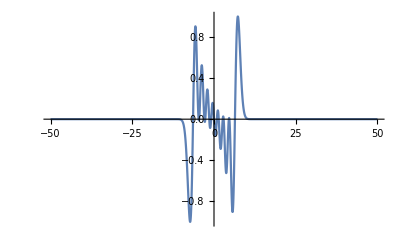

```mathematica
Plot[ϕ[6][p]H[9][p],{p,-50,50},PlotRange->All]
```